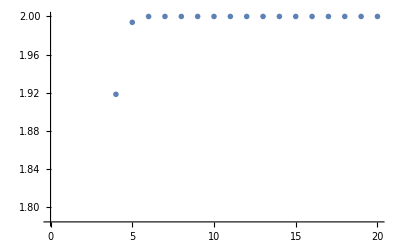

2.

```mathematica
x=1/2;
sum = 0;
an = {};
For[i=0,i≠ 20,i++;
sum+=1/(x+1);
an =Append[an,sum];
x*=(1+x);]
t=ListPlot[an,PlotRange->Automatic,PlotStyle->PointSize[0.01]];
Print [t]
N[sum,100]
```